```mathematica
h = 6.6261963*10^-35 (*Jerk-sh*)
```

6.6262×10^-35

```mathematica
k=1.6021917*10^-25 (*Jrk/keV*)
```

1.60219×10^-25

```mathematica
c = 299.792458 (*cm/sh*)
```

299.792

```mathematica
B[ν_,T_]:= (2 k^4 ν^3)/(h^3c^2) 1/(Exp[ν/(T)]-1) (*Clark,JCP 70,no.2 1987,p 316*)
```

```mathematica
OpacData = Import["/Users/ryanmcclarren/Dropbox/Papers/IMC/MMC/Aluminum50groups.csv"]
```

{{0.001,1.×10^10,1.×10^10},{0.001229,1.×10^10,1.×10^10},{0.0015104,1.×10^10,1.×10^10},{0.0018562,1.×10^10,1.×10^10},{0.0022812,1.×10^10,1.×10^10},{0.0028036,1.×10^10,1.×10^10},{0.0034455,1.×10^10,1.×10^10},{0.0042344,1.×10^10,1.×10^10},{0.005204,1.×10^10,1.×10^10},{0.0063956,1.×10^10,1.×10^10},{0.00786,1.×10^10,1.×10^10},{0.0096598,1.×10^10,1.×10^10},{0.011872,1.×10^10,1.×10^10},{0.01459,1.×10^10,1.×10^10},{0.017931,1.×10^10,1.×10^10},{0.022036,8932.1,8932.6},{0.027082,8561.5,8569.},{0.033283,7307.1,7334.8},{0.040904,5610.5,5655.9},{0.05027,3984.1,4031.},{0.06178,2671.3,2710.5},{0.075926,1742.3,1769.8},{0.093311,1174.7,1184.4},{0.11468,778.38,792.36},{0.14093,497.78,506.05},{0.17321,317.6,322.98},{0.21286,202.84,206.18},{0.2616,172.36,209.98},{0.32151,108.33,122.94},{0.39512,75.001,75.79},{0.48559,48.333,49.048},{0.59678,30.697,31.1},{0.73343,19.245,19.467},{0.90136,11.878,11.961},{1.1078,7.2577,7.249},{1.3614,4.7417,5.3814},{1.6731,5.9804,67.779},{2.0562,19.961,21.13},{2.527,12.861,13.033},{3.1057,7.6712,7.7358},{3.8168,4.4875,4.4471},{4.6907,2.6193,2.5158},{5.7648,1.5464,1.407},{7.0847,0.94072,0.78179},{8.707,0.60199,0.43257},{10.701,0.41258,0.2385},{13.151,0.30609,0.13092},{16.162,0.24517,0.071433},{19.863,0.2094,0.03867},{24.411,0.18752,0.020756}}

```mathematica
CForm[OpacData[[;;,3]]]
```

List(1.e10,1.e10,1.e10,1.e10,1.e10,1.e10,1.e10,1.e10,1.e10,1.e10,1.e10,1.e10,1.e10,1.e10,1.e10,8932.6,8569.,7334.8,5655.9,
   4031.,2710.5,1769.8,1184.4,792.36,506.05,322.98,206.18,209.98,122.94,75.79,49.048,31.1,19.467,11.961,7.249,5.3814,67.779,
   21.13,13.033,7.7358,4.4471,2.5158,1.407,0.78179,0.43257,0.2385,0.13092,0.071433,0.03867,0.020756)

```mathematica
nbins=Dimensions[OpacData][[1]]
```

50

```mathematica
tb[Z_,μ_,v_,t_,L_]:=Max[ (μ c t - Z)/(μ c - v),0]
```

```mathematica
tf[Z_,μ_,v_,t_,L_]:=Max[ (L+(μ c t - Z))/(μ c - v),0]
```

```mathematica
s[Z_,μ_,v_,t_,L_]:=Max[c*(tf[Z,μ,v,t,L]-tb[Z,μ,v,t,L]) ,0]
```

```mathematica
logspace[a_,b_,n_]:=Exp[Range[a,b,(b-a)/(n-1)]]
```

```mathematica
groupBounds=Table[If[i≤ nbins,OpacData[[i,1]],30],{i,1,nbins+1}];
groupWidths = Differences[groupBounds];
groupGmid=Table[GeometricMean[groupBounds[[i;;i+1]]],{i,1,nbins}];
```

```mathematica
CForm[groupGmid]
```

List(0.001108602724153247,0.0013624542561128429,0.00167439675107186,0.0020577568952624115,0.002528946879631915,
   0.003108022490266118,0.0038196367890154163,0.004694232376012079,0.00576911625814561,0.007090092806162696,
   0.008713554269068393,0.010708928312394289,0.013161021236970938,0.016174464133318297,0.01987781466861989,
   0.02442905958075341,0.030022828081311726,0.03689726049451368,0.04534582759196264,0.055728633573774264,0.06848874564481379,
   0.08417084403758822,0.10344518103807447,0.1271292743627525,0.15623855254065816,0.19201427186540065,0.2359749478228568,
   0.2900120962994475,0.3564197401940583,0.4380254796241881,0.5383218370083086,0.661586241846065,0.8130710084611307,
   0.9992630324394073,1.2280712194331402,1.5092244167121072,1.854785222067504,2.2794774401164846,2.8014467512340833,
   3.4429399878592135,4.2312484871489175,5.20009109150984,6.390765099735711,7.854074286636204,9.652647667868129,
   11.862919160139295,14.578973283465471,17.917193027927116,22.01989311963162,27.06159640523818)

```mathematica
Tval = 1 (*keV*)
```

1

```mathematica
dens = 1/10 (*g/cc*)
```

1/10

```mathematica
OpacData[[32-1,3]]
```

49.048

```mathematica
N[groupBounds]
```

{0.001,0.001229,0.0015104,0.0018562,0.0022812,0.0028036,0.0034455,0.0042344,0.005204,0.0063956,0.00786,0.0096598,0.011872,0.01459,0.017931,0.022036,0.027082,0.033283,0.040904,0.05027,0.06178,0.075926,0.093311,0.11468,0.14093,0.17321,0.21286,0.2616,0.32151,0.39512,0.48559,0.59678,0.73343,0.90136,1.1078,1.3614,1.6731,2.0562,2.527,3.1057,3.8168,4.6907,5.7648,7.0847,8.707,10.701,13.151,16.162,19.863,24.411,30.}

```mathematica
opacsGmid=Table[Evaluate[σ[groupGmid[[j]],Tval]],{j,1,nbins}];
```

Part::pkspec1: The expression j cannot be used as a part specification.

```mathematica
pcf = Table[{OpacData[[i,3]],ν>groupBounds[[i]]&& ν≤ groupBounds[[i+1]]},{i,1,50}];
opacPiece = Piecewise[pcf];
```

```mathematica
opacfunc[νt_]:=opacPiece/.ν->νt
```

```mathematica
{groupBounds[[i]],groupGmid[[i]],groupBounds[[i+1]]}/.i->50
```

Part::pkspec1: The expression i cannot be used as a part specification.

Part::pkspec1: The expression 1+i cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

{24.411,27.0616,30}

```mathematica
OpacData[[50,3]]
```

0.020756

```mathematica
opacfunc[groupGmid[[49]]]
```

0.03867

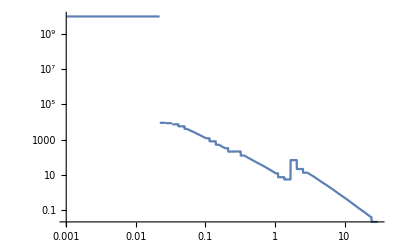

```mathematica
LogLogPlot[{opacfunc[x]+0*B[x,Tval]*200},{x,0.001,30}]
```

```mathematica
Iz[Z_,μ_,ν_,v_,t_,L_,T_,dens_]:= B[γ Dl ν, T]/(γ Dl)^3(1-Exp[-γ Dl (dens*opacfunc[ν*γ*Dl]) s[Z,μ,v,t,L]])/.{Dl-> 1-μ v/c,γ-> 1/Sqrt[(1-β^2)]}/.{β-> v/c}/.{L->L}
```

```mathematica
IzNoMult[Z_,μ_,ν_,v_,t_,L_,T_,dens_]:= B[ν, T]/(γ Dl)^3(1-Exp[-γ Dl (dens*opacfunc[ν]) s[Z,μ,v,t,L]])/.{Dl-> 1-μ v/c,γ-> 1/Sqrt[(1-β^2)]}/.{β-> v/c}/.{L->L}
```

```mathematica
spectrum=Table[{N[groupGmid[[i]]],NIntegrate[Evaluate[Iz[12,μ,T,5.994,1,4/10,Tval,dens]],{μ,0,1},{T,groupBounds[[i]],groupBounds[[i+1]]},PrecisionGoal->12, MaxRecursion->40,Method->"GlobalAdaptive"]*2π/c*1/groupWidths[[i]]},{i,1,50}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.34683×10^-11 and 3.53001×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000119444 and 5.94935×10^-15 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000215582 and 1.8196×10^-15 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{{0.0011086,1.23264×10^-9},{0.00136245,1.93025×10^-9},{0.0016744,2.91486×10^-9},{0.00205776,4.40156×10^-9},{0.00252895,6.64657×10^-9},{0.00310802,1.00359×10^-8},{0.00381964,1.51523×10^-8},{0.00469423,2.28757×10^-8},{0.00576912,3.45326×10^-8},{0.00709009,5.21227×10^-8},{0.00871355,7.86612×10^-8},{0.0107089,1.18694×10^-7},{0.013161,1.79051×10^-7},{0.0161745,2.70025×10^-7},{0.0198778,4.07071×10^-7},{0.0244291,6.13416×10^-7},{0.0300228,9.23892×10^-7},{0.0368973,1.3906×10^-6},{0.0453458,2.0914×10^-6},{0.0557286,3.14225×10^-6},{0.0684887,4.7154×10^-6},{0.0841708,7.06558×10^-6},{0.103445,0.0000105679},{0.127129,0.0000157689},{0.156239,0.0000234645},{0.192014,0.0000347925},{0.235975,0.0000513616},{0.290012,0.0000754175},{0.35642,0.000109875},{0.438025,0.00015748},{0.538322,0.000218804},{0.661586,0.00028822},{0.813071,0.000353783},{0.999263,0.000399677},{1.22807,0.000413646},{1.50922,0.000442703},{1.85479,0.00117913},{2.27948,0.00115147},{2.80145,0.00101524},{3.44294,0.000755801},{4.23125,0.000458824},{5.20009,0.000221357},{6.39077,0.000081788},{7.85407,0.0000221748},{9.65265,4.20577×10^-6},{11.8629,5.24823×10^-7},{14.579,4.00099×10^-8},{17.9172,1.69775×10^-9},{22.0199,3.54428×10^-11},{27.0616,3.14238×10^-13}}

```mathematica
Export["/Users/ryanmcclarren/Dropbox/Papers/IMC/MMC/AlSlabNominal.csv",spectrum]
```

/Users/ryanmcclarren/Dropbox/Papers/IMC/MMC/AlSlabNominal.csv

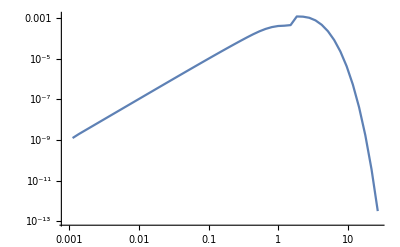

```mathematica
ListLogLogPlot[spectrum,Joined->True]
```

```mathematica
spectrumNoV=Table[{N[groupGmid[[i]]],NIntegrate[Evaluate[IzNoMult[12,μ,T,5.994,1,4/10,Tval,dens]],{μ,0,1},{T,groupBounds[[i]],groupBounds[[i+1]]},PrecisionGoal->12, MaxRecursion->40,Method->"GlobalAdaptive"]*2π/c*1/groupWidths[[i]]},{i,1,50}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{0.0011086,1.30478×10^-9},{0.00136245,1.97048×10^-9},{0.0016744,2.9756×10^-9},{0.00205776,4.49328×10^-9},{0.00252895,6.78504×10^-9},{0.00310802,1.0245×10^-8},{0.00381964,1.54679×10^-8},{0.00469423,2.33521×10^-8},{0.00576912,3.52515×10^-8},{0.00709009,5.32074×10^-8},{0.00871355,8.02975×10^-8},{0.0107089,1.21162×10^-7},{0.013161,1.82772×10^-7},{0.0161745,2.75631×10^-7},{0.0198778,4.15515×10^-7},{0.0244291,6.26125×10^-7},{0.0300228,9.43006×10^-7},{0.0368973,1.41932×10^-6},{0.0453458,2.1345×10^-6},{0.0557286,3.20683×10^-6},{0.0684887,4.81198×10^-6},{0.0841708,7.2097×10^-6},{0.103445,0.0000107823},{0.127129,0.0000160868},{0.156239,0.0000239338},{0.192014,0.0000354815},{0.235975,0.0000523658},{0.290012,0.0000768688},{0.35642,0.000111937},{0.438025,0.000160261},{0.538322,0.000222197},{0.661586,0.000291653},{0.813071,0.000356431},{0.999263,0.000400809},{1.22807,0.000413113},{1.50922,0.000443244},{1.85479,0.0012222},{2.27948,0.00114155},{2.80145,0.00100489},{3.44294,0.000741969},{4.23125,0.000446553},{5.20009,0.000213661},{6.39077,0.0000782811},{7.85407,0.000021018},{9.65265,3.9309×10^-6},{11.8629,4.82364×10^-7},{14.579,3.60084×10^-8},{17.9172,1.48427×10^-9},{22.0199,2.99146×10^-11},{27.0616,2.53658×10^-13}}

```mathematica
Export["/Users/ryanmcclarren/Dropbox/Papers/IMC/MMC/AlSlabNoDopplerNu.csv",spectrumNoV]
```

/Users/ryanmcclarren/Dropbox/Papers/IMC/MMC/AlSlabNoDopplerNu.csv

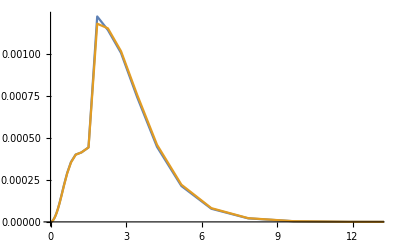

```mathematica
ListPlot[{spectrumNoV,spectrum},Joined->True]
```

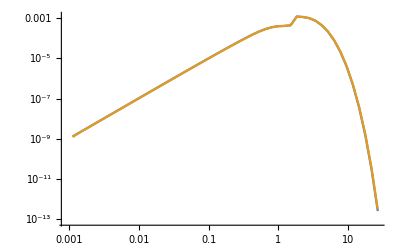

```mathematica
ListLogLogPlot[{spectrumNoV,spectrum},Joined->True]
```

```mathematica
Diff = Table[{spectrum[[i,1]],(spectrumNoV[[i,2]]-spectrum[[i,2]])/spectrum[[i,2]]},{i,1,nbins-19}]
```

{{0.0011086,0.0585265},{0.00136245,0.0208405},{0.0016744,0.0208389},{0.00205776,0.0208369},{0.00252895,0.0208344},{0.00310802,0.0208313},{0.00381964,0.0208275},{0.00469423,0.0208229},{0.00576912,0.0208172},{0.00709009,0.0208102},{0.00871355,0.0208017},{0.0107089,0.0207911},{0.013161,0.0207781},{0.0161745,0.0207621},{0.0198778,0.0207424},{0.0244291,0.0207182},{0.0300228,0.0206884},{0.0368973,0.0206517},{0.0453458,0.0206065},{0.0557286,0.0205508},{0.0684887,0.0204821},{0.0841708,0.0203972},{0.103445,0.0202923},{0.127129,0.0201625},{0.156239,0.0200017},{0.192014,0.019802},{0.235975,0.0195515},{0.290012,0.0192438},{0.35642,0.0187696},{0.438025,0.0176583},{0.538322,0.015504}}

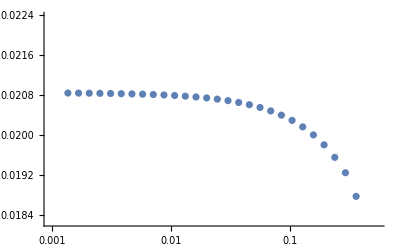

```mathematica
ListLogLinearPlot[Diff]
```

```mathematica
spectrumStationary=Table[{N[groupGmid[[i]]],NIntegrate[Evaluate[Iz[12,μ,T,0*5.994,1,4/10,Tval,dens]],{μ,0,1},{T,groupBounds[[i]],groupBounds[[i+1]]},PrecisionGoal->12, MaxRecursion->40,Method->"GlobalAdaptive"]*2π/c*1/groupWidths[[i]]},{i,1,50}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{0.0011086,1.26508×10^-9},{0.00136245,1.91052×10^-9},{0.0016744,2.88506×10^-9},{0.00205776,4.35654×10^-9},{0.00252895,6.57857×10^-9},{0.00310802,9.93324×10^-9},{0.00381964,1.49972×10^-8},{0.00469423,2.26414×10^-8},{0.00576912,3.41788×10^-8},{0.00709009,5.15883×10^-8},{0.00871355,7.7854×10^-8},{0.0107089,1.17475×10^-7},{0.013161,1.7721×10^-7},{0.0161745,2.67244×10^-7},{0.0198778,4.0287×10^-7},{0.0244291,6.07071×10^-7},{0.0300228,9.1431×10^-7},{0.0368973,1.37613×10^-6},{0.0453458,2.06955×10^-6},{0.0557286,3.10925×10^-6},{0.0684887,4.66555×10^-6},{0.0841708,6.9903×10^-6},{0.103445,0.0000104542},{0.127129,0.0000155973},{0.156239,0.0000232055},{0.192014,0.0000344017},{0.235975,0.0000507721},{0.290012,0.0000745294},{0.35642,0.000108528},{0.438025,0.000155358},{0.538322,0.000215292},{0.661586,0.000282225},{0.813071,0.000343997},{0.999263,0.000384945},{1.22807,0.000393453},{1.50922,0.000419094},{1.85479,0.00118471},{2.27948,0.00110238},{2.80145,0.00096614},{3.44294,0.000707602},{4.23125,0.000419792},{5.20009,0.000196321},{6.39077,0.0000698485},{7.85407,0.0000182207},{9.65265,3.33114×10^-6},{11.8629,4.02499×10^-7},{14.579,2.97594×10^-8},{17.9172,1.21977×10^-9},{22.0199,2.45044×10^-11},{27.0616,2.07409×10^-13}}

```mathematica
Export["/Users/ryanmcclarren/Dropbox/Papers/IMC/MMC/AlSlabNoV.csv",spectrumStationary]
```

/Users/ryanmcclarren/Dropbox/Papers/IMC/MMC/AlSlabNoV.csv

```mathematica
CForm[spectrumNoV]
```

List(List(0.001108602724153247,1.305036649062918e-9),List(0.0013624542561128429,1.970866739385328e-9),
   List(0.00167439675107186,2.9761893437564184e-9),List(0.0020577568952624115,4.493355875577325e-9),
   List(0.002528946879631915,6.78551238618812e-9),List(0.003108022490266118,1.0246296711878912e-8),
   List(0.0038196367890154163,1.547086996282998e-8),List(0.004694232376012079,2.3356646546953346e-8),
   List(0.00576911625814561,3.525844940811253e-8),List(0.007090092806162696,5.3217857454520266e-8),
   List(0.008713554269068393,8.031329691842306e-8),List(0.010708928312394289,1.211855435057229e-7),
   List(0.013161021236970938,1.8280772256785573e-7),List(0.016174464133318297,2.756469386921274e-7),
   List(0.01987781466861989,4.1556303501806054e-7),List(0.02442905958075341,6.26239439485376e-7),
   List(0.030022828081311726,9.431912775089957e-7),List(0.03689726049451368,1.4195978708658289e-6),
   List(0.04534582759196264,2.1349202991210183e-6),List(0.055728633573774264,3.207461445921713e-6),
   List(0.06848874564481379,4.812927159880988e-6),List(0.08417084403758822,7.209817291822186e-6),
   List(0.10344518103807447,0.000010783148891448124),List(0.1271292743627525,0.000016089213064661025),
   List(0.15623855254065816,0.000023938533408023),List(0.19201427186540065,0.000035488542655153936),
   List(0.2359749478228568,0.00005237625088066594),List(0.2900120962994475,0.00007688416731756187),
   List(0.3564197401940583,0.00011195946979359446),List(0.4380254796241881,0.0001602756786596657),
   List(0.5383218370083086,0.00022224526457801213),List(0.661586241846065,0.0002917238355966859),
   List(0.8130710084611307,0.000356405972586116),List(0.9493998104065536,0.0003705390194684365),
   List(1.0069756700139283,0.00040079968608355463),List(1.0210256607940862,0.0004028399073427481),
   List(1.0352749634758873,0.0004047126571133877),List(1.0497249639786603,0.0004064502972983214),
   List(1.064374276276912,0.00040802009343653405),List(1.079224286235257,0.00040940247731905544),
   List(1.0942736083813773,0.00041057899509596395),List(1.1095732828434541,0.0004115346273709214),
   List(1.12507296207846,0.0004122260499495457),List(1.140772646060555,0.0004126273897492443),
   List(1.1566723347603678,0.00041271228402943016),List(1.1728216829509932,0.00041265139573842086),
   List(1.1892213839315202,0.0004126257201551967),List(1.2058210895485284,0.0004125689872019527),
   List(1.2226207997576355,0.0004124266739984377),List(1.2396701698435757,0.0004121776139820726),
   List(1.257019546387406,0.0004118093090077589),List(1.2745696214801294,0.0004112517113337728),
   List(1.2923190086042997,0.00041048310073497793),List(1.310368402396822,0.00040956798048162667),
   List(1.3286681489371226,0.0004084935465388073),List(1.3472175548143663,0.0004072278837668289),
   List(1.3660173132138553,0.0004057423638066034),List(1.385066731244383,0.000404008353772547),
   List(1.4044161562727766,0.0004020278645334379),List(1.4240655883771645,0.00039979319005391804),
   List(1.4439653735460556,0.0003972469518036509),List(1.4641148179019294,0.00039440451981203847),
   List(1.4845146142763297,0.0003916156103920715),List(1.5052137256881495,0.00038897769164272084),
   List(1.5262631915891833,0.0003866008665240128),List(1.5475630100257631,0.0003847889126562726),
   List(1.569162142673599,0.0004017716822354882),List(1.591061975537094,0.0007886454917714136),
   List(1.6132611226952691,0.000443355479768182),List(1.6358106247362498,0.00038160530502349624),
   List(1.6586601339635556,0.00038886177432044143),List(1.6818096503469113,0.0004539165612598653),
   List(1.705259173850122,0.0010485773070992052),List(1.7290583593389786,0.0011682408337392134),
   List(1.753207899822494,0.0008729332953991113),List(1.7777071018590211,0.00043766439777894194),
   List(1.8025070041472793,0.0003938921320245202),List(1.8276558757052708,0.0003960865111211545),
   List(1.8532054500243627,0.00044515974145802306),List(1.879055031126018,0.0004756627808314828),
   List(1.9052542743686471,0.0004510909032092086),List(1.9318535270563346,0.00047932691294500646),
   List(1.9588527892621233,0.0005254546679891628),List(1.9838672460625988,0.0006458070978934401),
   List(2.041759116546318,0.0012690153211877698),List(2.137982820323868,0.001104707753866907),
   List(2.238756578996475,0.0011592241997452509),List(2.344229280595224,0.001130351933741751),
   List(2.4546987024887597,0.0011052458504995748),List(2.5704183647803327,0.001080889533946127),
   List(2.6915371556045815,0.0010487481126564091),List(2.8183528522880166,0.0010057860818690606),
   List(2.9512166982449797,0.0009509616848441513),List(3.090331050227467,0.0008923651562890736),
   List(3.23594251957602,0.0008326712283495267),List(3.3884512125748545,0.0007694333056260341),
   List(3.5481595116341653,0.0007015394336201861),List(3.7153651933558294,0.0006294792597055002),
   List(3.8904683638348736,0.0005613400775555531),List(4.0738202672675685,0.0004980780551866056),
   List(4.2658187068838265,0.0004369764541992307),List(4.466866091568002,0.00037719349167321),
   List(4.6773602245283605,0.00031933940450590254),List(4.8978012383109215,0.0002684708985948666),
   List(5.128640403654754,0.0002244040012749327),List(5.370326688386843,0.00018503234924222456),
   List(5.623409087021858,0.00014961850057455443),List(5.8884388966856065,0.00011820663026778653),
   List(6.165965111805288,0.0000926180168730352),List(6.456539029542066,0.00007205668945612517),
   List(6.760807368206848,0.00005513846407707139),List(7.079472615950993,0.00004121632337113213),
   List(7.413134931997393,0.00002997950129299168),List(7.7624921990298965,0.000021590309406092806),
   List(8.128295767256505,0.000015409089216147963),List(8.511343546115384,0.000010781705587401024),
   List(8.912486912192355,7.3392145102110614e-6),List(9.332526077649074,4.8391424732408405e-6),
   List(10.10907908268602,2.52167940407069e-6),List(11.862919160139295,4.823927021362135e-7),
   List(14.578973283465471,3.6011480504476873e-8),List(17.917193027927116,1.484419800359805e-9),
   List(22.01989311963162,2.9915954298550494e-11),List(27.06159640523818,2.5367498823629386e-13))